## The dumb approach

```mathematica
HF[t_]:=ⅇ^(-(t^2+1)/t)1/(2BesselK[1,2])
```

```mathematica
N[1/(2BesselK[1,2]) ,32]
```

3.5748532344428743120454466520221

```mathematica
Integrate[HF[t],{t,0,∞}]
```

1

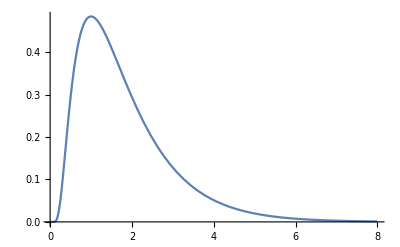

```mathematica
Plot[HF[t],{t,10^-2,8},PlotRange->All]
```

```mathematica
NIntegrate[HF[x/(1-x)] 1/(1-x)^2,{x,0,1}]
```

1.

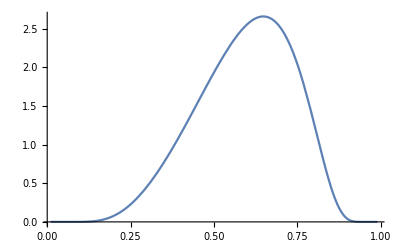

```mathematica
Plot[HF[x/(1-x)] 1/(1-x)^2,{x,10^-2,1-10^-2}]
```

```mathematica
monitoredFindRoot[args__] := Module[{s = 0, e = 0,j = 0},
{FindRoot[args, StepMonitor:>s++,EvaluationMonitor:>e++,Jacobian->{Automatic,EvaluationMonitor:>j++}],"Steps"->s,"Evaluations"->e,"Jacobian Evaluations"->j}]
```

```mathematica
leftBinTest=0.6;
monitoredFindRoot[Integrate[HF[x/(1-x)] 1/(1-x)^2,{x,leftBinTest,leftBinTest+b}]-1/10,{b,0.1,0.,0.5},PrecisionGoal->16(*,Method->"Brent"*)]
```

{{b→0.0382152},Steps→4,Evaluations→5,Jacobian Evaluations→4}

```mathematica
leftBinTest=0.0;
monitoredFindRoot[Integrate[HF[x/(1-x)] 1/(1-x)^2,{x,leftBinTest,leftBinTest+b}]-1/10,{b,0.1,0.,0.5},PrecisionGoal->16(*,Method->"Brent"*)]
```

{{b→0.396009},Steps→11,Evaluations→18,Jacobian Evaluations→11}

```mathematica
PreviousBinBoundary=0.;
NBins=10;
BinLeftEdges = {0.};
For[iBin=1,iBin<NBins,iBin++,
Print["Computing right edge of bin #"<>ToString[iBin]<>"..."];
AppendTo[
BinLeftEdges,
(BinLeftEdges⟦-1⟧+b)/.(FindRoot[(Integrate[HF[x/(1-x)] 1/(1-x)^2,{x,BinLeftEdges⟦-1⟧,BinLeftEdges⟦-1⟧+b}]-1./NBins),{b,0.1,0.,0.5},PrecisionGoal->16])
];
Print["..."<>ToString[BinLeftEdges⟦-1⟧]];
];
```

Computing right edge of bin #1...

...0.396009

Computing right edge of bin #2...

...0.467879

Computing right edge of bin #3...

...0.520801

Computing right edge of bin #4...

...0.565322

Computing right edge of bin #5...

...0.605451

Computing right edge of bin #6...

...0.643488

Computing right edge of bin #7...

...0.681339

Computing right edge of bin #8...

...0.72147

Computing right edge of bin #9...

...0.769444

```mathematica
Export["~/Desktop/BinLeftEdges_10.csv",BinLeftEdges]
```

~/Desktop/BinLeftEdges_10.csv

```mathematica
rawTable=Import["~/Desktop/BinLeftEdges_10.csv"];
BinLeftEdges=Table[bin⟦1⟧ , {bin,rawTable}]
```

{0.,0.396009,0.467879,0.520801,0.565322,0.605451,0.643488,0.681339,0.72147,0.769444}

```mathematica
DummyBinLeftEdges=Join[BinLeftEdges,{1.}];
CDFchunks=Table[
NIntegrate[HF[x/(1-x)] 1/(1-x)^2,{x,DummyBinLeftEdges⟦iBin⟧,DummyBinLeftEdges⟦iBin+1⟧}],
{iBin,1,Length[DummyBinLeftEdges]-1}
]
Total[CDFchunks]
```

{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}

1.

```mathematica
DummyBinLeftEdges=Join[BinLeftEdges,{1.}];
ApproximatedPDFX[x_]:=Total[Table[
(HeavisideTheta[x-DummyBinLeftEdges⟦ib-1⟧]HeavisideTheta[DummyBinLeftEdges⟦ib⟧-x])
*(1/(Length[BinLeftEdges]*(DummyBinLeftEdges⟦ib⟧-DummyBinLeftEdges⟦ib-1⟧))),
{ib,2,Length[DummyBinLeftEdges]}
]]
```

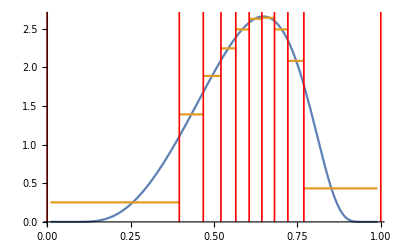

```mathematica
DummyBinLeftEdges=Join[BinLeftEdges,{1.}];
lineStyle={Thickness[0.003],Red};
Plot[
{
HF[x/(1-x)] 1/(1-x)^2,
ApproximatedPDFX[x]
},
{x,10^-2,1-10^-2}
,PlotRange->All,
Epilog->Join[{Directive[lineStyle]},Table[
Line[{{b,0},{b,3.5}}],
{b,DummyBinLeftEdges}
]]
]
```

```mathematica
DummyBinLeftEdges=Join[BinLeftEdges,{1.}];
ApproximatedPDFT[t_]:=Total[Table[
(HeavisideTheta[t/(1+t)-DummyBinLeftEdges⟦ib-1⟧]HeavisideTheta[DummyBinLeftEdges⟦ib⟧-t/(1+t)])
*(1/(Length[BinLeftEdges]*(DummyBinLeftEdges⟦ib⟧/Max[1-DummyBinLeftEdges⟦ib⟧,0.1]-DummyBinLeftEdges⟦ib-1⟧/(1-DummyBinLeftEdges⟦ib-1⟧)))),
{ib,2,Length[DummyBinLeftEdges]}
]]
```

```mathematica
ApproximatedPDFT[t_]:=1
```

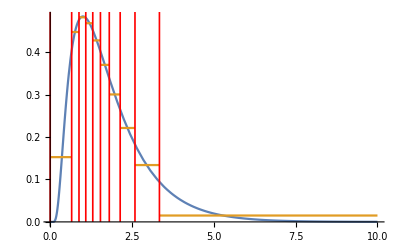

```mathematica
DummyBinLeftTEdges=Table[b/(1-b),{b,BinLeftEdges}];
lineStyle={Thickness[0.003],Red};
Plot[
{
HF[t],
ApproximatedPDFT[t]
},
{t,10^-2,10}
,PlotRange->All,
Epilog->Join[{Directive[lineStyle]},Table[
Line[{{b,0},{b,0.5}}],
{b,DummyBinLeftTEdges}
]]
]
```

```mathematica
DummyBinLeftEdges=Join[BinLeftEdges,{1.}];
LinearApproximatedPDFX[x_]:=Total[Table[
(HeavisideTheta[x-DummyBinLeftEdges⟦ib-1⟧]HeavisideTheta[DummyBinLeftEdges⟦ib⟧-x])
*(
1/(Length[BinLeftEdges]*(DummyBinLeftEdges⟦ib⟧-DummyBinLeftEdges⟦ib-1⟧))
),
{ib,2,Length[DummyBinLeftEdges]}
]]
```

## Linear PDF interpolation

```mathematica
HF[t_]:=ⅇ^(-(t^2+1)/t)1/(2BesselK[1,2])
```

```mathematica
N[1/(2BesselK[1,2]) ,32]
```

3.5748532344428743120454466520221

```mathematica
Integrate[HF[t],{t,0,∞}]
```

1

```mathematica
Plot[HF[t],{t,10^-2,8},PlotRange->All]
```

-Graphics-

```mathematica
HFX[x_]:=If[Or[x==0,x==1],0,HF[x/(1-x)] 1/(1-x)^2]
```

```mathematica
NIntegrate[HFX[x],{x,0,1}]
```

1.

```mathematica
Plot[HFX[x],{x,10^-2,1-10^-2}]
```

-Graphics-

```mathematica
NBins=10;
```

```mathematica
Bins=Table[<|"left_edge"->N[(ib-1)*1/NBins],"right_edge"->N[ib*1/NBins]|>,{ib,NBins}];
```

```mathematica
UpdateBinInfo[bid_,OptionsPattern[{UpdatePDFInterpol->True}]]:=Module[{
leftEdge,rightEdge,leftEval,rightEval,leftCDF,rightCDF
},
leftEdge=Bins⟦bid⟧["left_edge"];
rightEdge=Bins⟦bid⟧["right_edge"];
If[OptionValue["UpdatePDFInterpol"],
leftEval=HFX[leftEdge];
rightEval=HFX[rightEdge];
AssociateTo[Bins⟦bid⟧,"b"->leftEval-(rightEval-leftEval)/(rightEdge-leftEdge)leftEdge];
AssociateTo[Bins⟦bid⟧,"a"->(rightEval-leftEval)/(rightEdge-leftEdge)];
];
leftCDF=If[bid==1,
0.,
Bins⟦bid-1⟧["CDF_right"]];
AssociateTo[Bins⟦bid⟧,"CDF_left"->leftCDF];
rightCDF=1/2 Bins⟦bid⟧⟦"a"⟧*(rightEdge^2-leftEdge^2)+Bins⟦bid⟧⟦"b"⟧*(rightEdge-leftEdge)+leftCDF;
AssociateTo[Bins⟦bid⟧,"CDF_right"->rightCDF];
];
```

```mathematica
For[bid=1,bid≤Length[Bins],bid++,UpdateBinInfo[bid,UpdatePDFInterpol->True]];
```

```mathematica
CurrentCDFNorm=Bins⟦-1⟧["CDF_right"]
```

1.

```mathematica
NormalizeDistribution[bid_,Norm_]:=Module[{},
AssociateTo[Bins⟦bid⟧,"a"->Bins⟦bid⟧["a"]/Norm];
AssociateTo[Bins⟦bid⟧,"b"->Bins⟦bid⟧["b"]/Norm];
];
```

```mathematica
For[bid=1,bid≤Length[Bins],bid++,NormalizeDistribution[bid,CurrentCDFNorm]];
```

```mathematica
For[bid=1,bid≤Length[Bins],bid++,UpdateBinInfo[bid,UpdatePDFInterpol->False]];
```

```mathematica
InterpolatedPDFX[x_]:=Total[Table[
HeavisideTheta[x-bin⟦"left_edge"⟧]HeavisideTheta[bin⟦"right_edge"⟧-x](
bin⟦"a"⟧x+bin⟦"b"⟧
),
{bin,Bins}]]
```

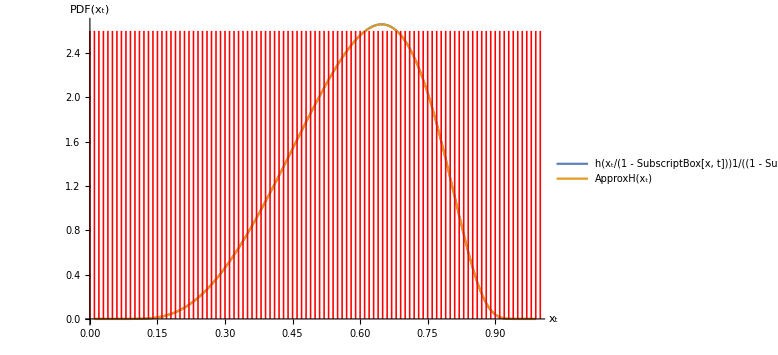

```mathematica
Plot[{HFX[x],InterpolatedPDFX[x]},{x,10^-2,1.-10^-2},
Epilog->Join[{Directive[{Thickness[0.002],Red}]},Table[
Line[{{bin⟦"left_edge"⟧,0},{bin⟦"left_edge"⟧,2.6}}],
{bin,Bins}
],
{Line[{{1.,0},{1.,2.6}}]}
],
AxesLabel->{"x_t","PDF(x_t)"},
PlotLegends->{"h(x_t/(1 - SubscriptBox[x, t]))1/(1 - SubscriptBox[x, t])^2","ApproxH(x_t)"},
ImageSize->Large
]
```

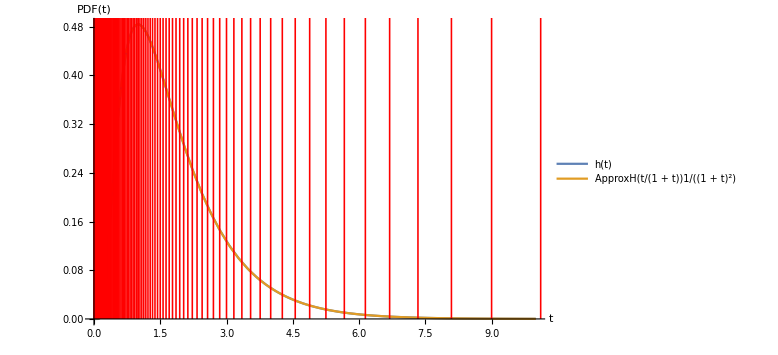

```mathematica
Plot[{HF[t],InterpolatedPDFX[t/(1+t)] 1/(1+t)^2},{t,10^-2,10},
Epilog->Join[{Directive[{Thickness[0.002],Red}]},Table[
Line[{{bin⟦"left_edge"⟧/(1-bin⟦"left_edge"⟧),0},{bin⟦"left_edge"⟧/(1-bin⟦"left_edge"⟧),2.6}}],
{bin,Bins}
],
{Line[{{1.,0},{1.,2.6}}]}
],
AxesLabel->{"t","PDF(t)"},
PlotLegends->{"h(t)","ApproxH(t/(1 + t))1/(1 + t)^2"},
ImageSize->Large
]
```

```mathematica
InterpolatedCDFX[x_]:=Total[Table[
HeavisideTheta[x-bin⟦"left_edge"⟧]HeavisideTheta[bin⟦"right_edge"⟧-x](
1/2 bin["a"](x)^2+bin⟦"b"⟧(x)-1/2 bin⟦"a"⟧(bin⟦"left_edge"⟧)^2-bin⟦"b"⟧(bin⟦"left_edge"⟧)+bin⟦"CDF_left"⟧
),
{bin,Bins}]]
```

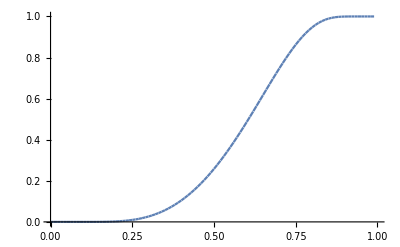

```mathematica
Plot[InterpolatedCDFX[x],{x,0,1}]
```

```mathematica
TSampler[rv_?NumericQ]:=Module[{ib,bin,a,b,c,xt, t, wgtT},
For[ib=1,ib≤Length[Bins],ib++,
If[Bins⟦ib⟧["CDF_left"]≤rv≤Bins⟦ib⟧["CDF_right"],bin=Bins⟦ib⟧]
];
a=1/2 bin["a"];
b=bin["b"];
c=-1/2 bin["a"](bin["left_edge"])^2-bin["b"](bin["left_edge"])+bin["CDF_left"]-rv;
xt=(-b+Sqrt[b^2-4a c])/(2 a);
t=xt/(1-xt);
wgtT=1./((bin["a"]xt+bin["b"])1/(1+t)^2);
<|"t"->t,"jacobian"->wgtT|>
]
```

```mathematica
Manipulate[TSampler[rv],{{rv,0.1},0.,1.}]
```

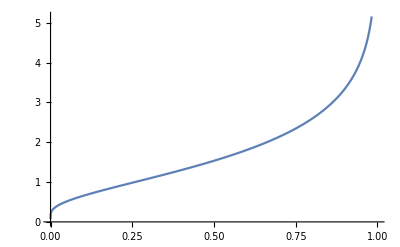

```mathematica
Plot[TSampler[rv]["t"],{rv,0,1}]
```

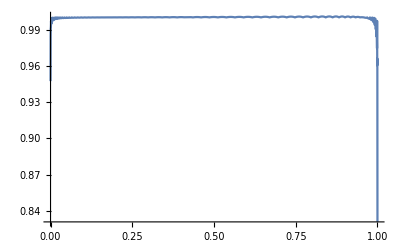

```mathematica
Plot[TSampler[rv]["jacobian"]*HF[TSampler[rv]["t"]],{rv,10^-5,1-10^-5},PlotRange->All]
```

```mathematica
NIntegrate[TSampler[rv]["jacobian"]*HF[TSampler[rv]["t"]],{rv,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rv near {rv} = {0.998767463347197989413650542900313666905276477336883544921875}. NIntegrate obtained 1.+6.96801×10^-13 ⅈ and 4.73332×10^-6 for the integral and error estimates.

1.